## BRDF Definitions

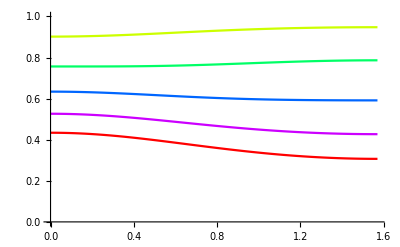

```mathematica
ggx[μ_,α_]:=α^2/(π(μ^2(α^2-1)+1)^2)
smith[θ_,α_]:=(2*Cos[θ])/(Cos[θ]+√(α^2+(1-α^2)*Cos[θ]^2))
lambda[θ_,α_]:=1/2(√(1+(α*Tan[θ])^2)-1)
smith2[θl_,θv_,α_]:=smith[θv,α] * smith[θl,α]
smith2[θl_,θv_,α_]:=(4*Cos[θl]*Cos[θv])/(2*Cos[θl]*√(Cos[θv]^2+α*Sin[θv]^2)+2*Cos[θv]*√(Cos[θl]^2+α*Sin[θl]^2))
smith2[θl_,θv_,α_]:=1/(1+lambda[θl,α]+lambda[θv,α])
(* change[] gives cos(Subscript[θ, h]) when provided with Subscript[ω, i] and Subscript[ω, o] *)
change[θo_,θi_,ϕi_]:=(Cos[θo]+Cos[θi])/(√(2*(1+Cos[θo]*Cos[θi]+Sin[θo]*Sin[θi]*Cos[ϕi])))
oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
BRDFggx[θo_,θi_,ϕi_,α_]:= (smith2[θo,θi,α]*ggx[change[θo,θi,ϕi],α])/(4*Cos[θo]*Cos[θi])

(*Eo[θo_,α_]:=smith[θo,α]*NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]*)
Eo[θo_,α_]:=NIntegrate[BRDFggx[θo,θi,ϕi,α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
Show[Table[Plot[Eo[Cos[θ],α],{θ,0,π/2},PlotRange->{0,1},PlotStyle->Hue[α]],{α,0.2, 1, 0.2}]]
```

1/(1+lambda+lamda)

smith*smith

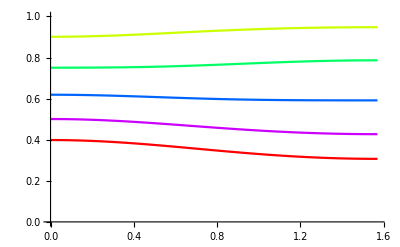

```mathematica
(*Manipulate[Plot[Eo[Cos[θ],α],{θ,0,π/2},PlotRange->{0,1}],{{α,1},0,1}]*)
```

Export (warning! SUPER LONG!)

```mathematica
countX = 128;
countY=128;
buildTable=Function[{i},
x=N[Mod[i,countX]/(countX-1)];
y=N[Quotient[i,countX]/(countY-1)];
θo=ArcCos[x];
α=Max[0.01,y];
{x,y,N[Eo[θo,α]]}
];
```

```mathematica
resultEo= Table[buildTable[i],{i,0,countX*countY-1}];
Export["MSBRDF_GGX_G2_E128x128.csv",resultEo,"CSV"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

MSBRDF_GGX_E128x128_G2.csv

Rebuild E_avg

```mathematica
t=Table[resultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}];
fEo=ListInterpolation[t,{{0,1},{0,1}}]
resultEavg=Table[{N[i/(countY-1)],2*π*NIntegrate[fEo[μ,i/(countY-1)]μ,{μ,0,1}]},{i,0,countY-1}]
Export["MSBRDF_GGX_G2_Eavg.csv",resultEavg,"CSV"]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

{{0.,3.13999},{0.00787402,3.13999},{0.015748,3.13798},{0.023622,3.13417},{0.0314961,3.12929},{0.0393701,3.12345},{0.0472441,3.11675},{0.0551181,3.10924},{0.0629921,3.101},{0.0708661,3.09207},{0.0787402,3.0825},{0.0866142,3.07233},{0.0944882,3.0616},{0.102362,3.05034},{0.110236,3.03858},{0.11811,3.02635},{0.125984,3.01368},{0.133858,3.00059},{0.141732,2.9871},{0.149606,2.97324},{0.15748,2.95904},{0.165354,2.9445},{0.173228,2.92965},{0.181102,2.91451},{0.188976,2.89909},{0.19685,2.88341},{0.204724,2.86748},{0.212598,2.85133},{0.220472,2.83496},{0.228346,2.81839},{0.23622,2.80163},{0.244094,2.7847},{0.251969,2.76761},{0.259843,2.75037},{0.267717,2.73299},{0.275591,2.71549},{0.283465,2.69786},{0.291339,2.68014},{0.299213,2.66231},{0.307087,2.6444},{0.314961,2.62642},{0.322835,2.60836},{0.330709,2.59025},{0.338583,2.57208},{0.346457,2.55388},{0.354331,2.53564},{0.362205,2.51737},{0.370079,2.49908},{0.377953,2.48078},{0.385827,2.46247},{0.393701,2.44416},{0.401575,2.42586},{0.409449,2.40758},{0.417323,2.38931},{0.425197,2.37106},{0.433071,2.35285},{0.440945,2.33466},{0.448819,2.31652},{0.456693,2.29842},{0.464567,2.28038},{0.472441,2.26238},{0.480315,2.24444},{0.488189,2.22656},{0.496063,2.20875},{0.503937,2.19101},{0.511811,2.17334},{0.519685,2.15574},{0.527559,2.13822},{0.535433,2.12079},{0.543307,2.10344},{0.551181,2.08618},{0.559055,2.069},{0.566929,2.05192},{0.574803,2.03494},{0.582677,2.01805},{0.590551,2.00126},{0.598425,1.98457},{0.606299,1.96798},{0.614173,1.9515},{0.622047,1.93512},{0.629921,1.91885},{0.637795,1.90269},{0.645669,1.88664},{0.653543,1.87071},{0.661417,1.85488},{0.669291,1.83917},{0.677165,1.82357},{0.685039,1.80809},{0.692913,1.79272},{0.700787,1.77748},{0.708661,1.76234},{0.716535,1.74733},{0.724409,1.73243},{0.732283,1.71766},{0.740157,1.703},{0.748031,1.68846},{0.755906,1.67404},{0.76378,1.65974},{0.771654,1.64556},{0.779528,1.6315},{0.787402,1.61756},{0.795276,1.60374},{0.80315,1.59004},{0.811024,1.57646},{0.818898,1.563},{0.826772,1.54966},{0.834646,1.53643},{0.84252,1.52333},{0.850394,1.51034},{0.858268,1.49747},{0.866142,1.48472},{0.874016,1.47208},{0.88189,1.45956},{0.889764,1.44716},{0.897638,1.43487},{0.905512,1.4227},{0.913386,1.41064},{0.92126,1.3987},{0.929134,1.38686},{0.937008,1.37514},{0.944882,1.36353},{0.952756,1.35204},{0.96063,1.34065},{0.968504,1.32937},{0.976378,1.3182},{0.984252,1.30714},{0.992126,1.29619},{1.,1.28534}}

MSBRDF_GGX_G2_Eavg.csv

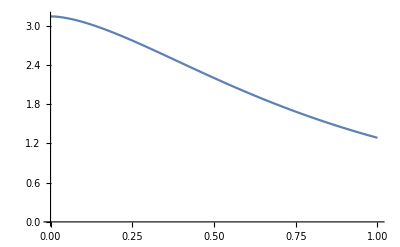

```mathematica
ListLinePlot[resultEavg]
```

## Tables Loading

Here, we want to make sure the irradiance tables computed by our MSBRDF notebook actually correspond to the magnitude values computed by the LTC fitter.
The temporary binary LTC file format I used contains 1 byte indicating whether the LTC is computed or not, then the 4 matrix elements m11, m22, m13 and m31 (double). Followed by the magnitude and fresnel integrated values (double). Followed by 3 vec3 values indicating the principal orientation of the M matrix (float). Finally followed by the error between the LTC and the actual BRDF (double).

```mathematica
(*LoadLTC=Function[{filename},
temp=BinaryReadList[filename,{ 
"Byte"
, "Real64", "Real64", "Real64", "Real64", "Real64", "Real64"
, "Real32", "Real32", "Real32"
, "Real32", "Real32", "Real32"
, "Real32", "Real32", "Real32"
, "Real64"}];(* Size of a single element = 1 + 7*8 + 9*4 = 93 *)
l=Length[temp];
s=N[Sqrt[l]];
N[l]
];*)

LoadLTC=Function[{filename},
(* Format contains Width and height as UINT32, followed by LTC elements *)
s=OpenRead[filename,BinaryFormat->True];
w=BinaryRead[s,"Integer32"];
h=BinaryRead[s,"Integer32"];

(* LTC elements are each a byte followed by the 6 double values + 3*3 floats describing a transform + a double representing the error between the BRDF and the LTC approximation *)
(* The table contains H rows where a row represents cos(θ)=1-y/H, y is the row index and θ is the view/light angle in [0,π/2] *)
(* The table contains W columns where a column represents α=(x/W)^2, x is the column index and α is the surface roughness in [0,1] *)
temp=Table[BinaryRead[s,{ 
"Byte"
, "Real64", "Real64", "Real64", "Real64", "Real64", "Real64"
, "Real32", "Real32", "Real32"
, "Real32", "Real32", "Real32"
, "Real32", "Real32", "Real32"
, "Real64"}],{i,1,w*h}];
(*temp=Table[ Table[x + y * 10,{i,1,6}],{x,1,w},{y,1,h}];*)
Close[s];
l=Length[temp];
temp
];
ltc=LoadLTC["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables\\GGX.ltc"];
```

```mathematica
(*mags=Table[ltc[[x]][[y]][[6]],{x,1,64},{y,1,64}];
ListPlot3D[mags,AxesLabel->{"X","Y","Z"}]*)
```

```mathematica
mags=Table[{ 1-(Quotient[i,64]/63)^2,(Mod[i,64]/63)^2, ltc[[1+i]][[6]]},{i,0,64*64-1}];
ListPlot3D[mags,AxesLabel->{"α","cos(θ)","Z"},PlotRange->{0.3,1}]
```

-Graphics3D-

### GGX

```mathematica
countX=128; countY=128;
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
resultEo = Import["MSBRDF_GGX_E128x128.csv","CSV"];
resultEo = Import["MSBRDF_GGX_E128x128_G2.csv","CSV"];

resultEavg=Import["MSBRDF_GGX_Eavg128.csv","CSV"];
fEo=ListInterpolation[Table[resultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}],{{0,1},{0,1}}];
fEavg=ListInterpolation[Table[resultEavg[[i]][[2]],{i,1,countY}],{0,1}];
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"},PlotRange->{0.3,1}]
Plot[fEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}];
```

-Graphics3D-

```mathematica
Show[
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"},PlotRange->{0.3,1}]
, ListPlot3D[mags,PlotStyle->Red]
]
```

-Graphics3D-